## Plots of stochastic data

```mathematica
SetDirectory["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social"];
```

```mathematica
data={Import["series_data/stoch_fun1_log.dat"],Import["series_data/stoch_fun1_lin.dat"],Import["series_data/stoch_fun1_cub.dat"]};
```

```mathematica
data//Dimensions
```

{3,4,1201}

```mathematica
(* time ticks *)
timeTicks=Table[{10(i-1),1800+10(i-1)},{i,1,130}];
(* max plot time *)
plotRange={200,300};
(* imgs size *)
imgs=350;
```

```mathematica
tVals=Table[i,{i,0,1200}];
```

```mathematica
(*legend=LineLegend[Table[TMBcolours[[i]],{i,1,3}],{"κ=0.005","κ=0.01","κ=0.02"}];*)
legend=LineLegend[Table[TMBcolours[[i]],{i,1,3}],{"logistic","linear","cubic"}];
```

```mathematica
(* emissions plot *)
emissionPlot=ListLinePlot[Table[Transpose[{tVals,data[[j,1]]}],{j,1,3}],
PlotRange->{plotRange,All},
FrameTicks->{{Automatic,None},{timeTicks[[1;;;;2]],None}},
ImageSize->imgs,
Frame->True,
LabelStyle->14,
FrameLabel->{{"CO_2emissions (gtC yr^-1)",None},{"Year",None}}];
```

```mathematica
(* temp plot *)
tempPlot=ListLinePlot[Table[Transpose[{tVals,data[[j,3]]}],{j,1,3}],
PlotRange->{plotRange,All},
FrameTicks->{{Automatic,None},{timeTicks[[1;;;;2]],None}},
ImageSize->imgs,
Frame->True,
LabelStyle->14,
(*PlotLegends->Placed[legend=legend,Scaled[{0.8,0.5}]]*)
FrameLabel->{{"Temperature (K)",None},{"Year",None}}];
```

```mathematica
(* cat plot *)
catPlot=ListLinePlot[Table[Transpose[{tVals,data[[j,2]]}],{j,1,3}],
PlotRange->{plotRange,All},
FrameTicks->{{Automatic,None},{timeTicks[[1;;;;2]],None}},
ImageSize->imgs,
Frame->True,
LabelStyle->14,
(*PlotLegends->Placed[legend=legend,Scaled[{0.8,0.5}]]*)
FrameLabel->{{"Atmospheric CO_2 (ppmv)",None},{"Year",None}}];
```

```mathematica
(* soc plot *)
socPlot=ListLinePlot[Table[Transpose[{tVals,data[[j,4]]}],{j,1,3}],
PlotRange->{plotRange,All},
FrameTicks->{{Automatic,None},{timeTicks[[1;;;;2]],None}},
ImageSize->imgs,
Frame->True,
LabelStyle->14,
PlotLegends->Placed[legend=legend,Scaled[{0.8,0.5}]],
FrameLabel->{{"Proportion mitigators",None},{"Year",None}}];
```

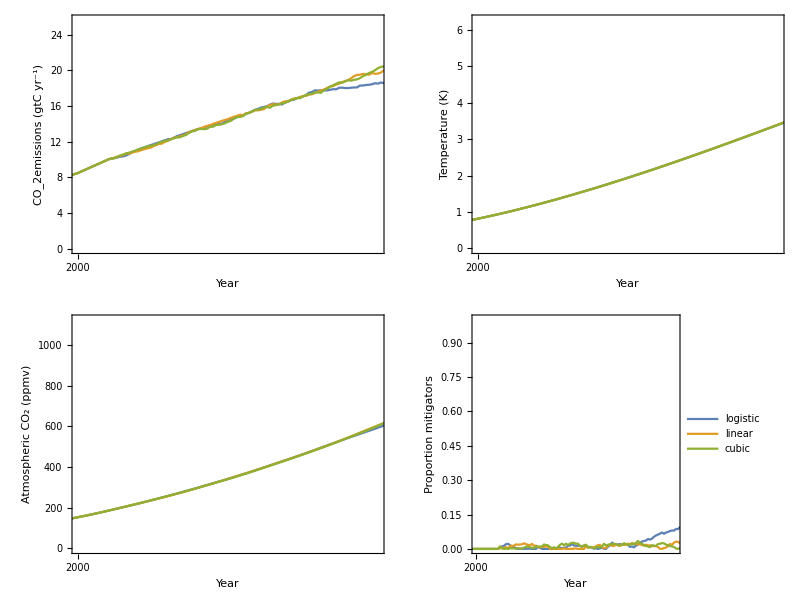

```mathematica
plotGrid=Grid[{{emissionPlot,tempPlot},{catPlot,socPlot}}]
```

```mathematica
(*Export["figures/social_stoch_fun.png",plotGrid];*)
```